```mathematica
SetDirectory["~/doc/research/first_order_singularities/paper"];
```

```mathematica
<<IsingScalingFunction`
```

```mathematica
data2={θ0->1.14841,θYL->0.989667,CYL->-0.172824,G[1]->-0.310183,G[2]->0.247454,g[0]->0.373691,g[1]->-0.0216363}
```

{θ0→1.14841,θYL→0.989667,CYL→-0.172824,G[1]→-0.310183,G[2]→0.247454,g[0]→0.373691,g[1]→-0.0216363}

```mathematica
prep2={θ0,θYL,ruleB[θ0,{g[0],g[1]}],ruleAL[θ0,{g[0],g[1]}],CYL,{G[1],G[2]},{g[0],g[1]}}/.data2
```

{1.14841,0.989667,5.08816,-0.0114291,-0.172824,{-0.310183,0.247454},{0.373691,-0.0216363}}

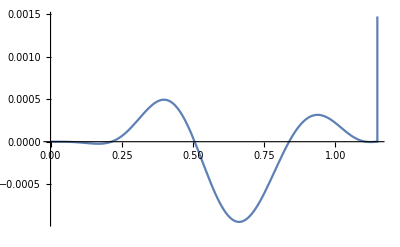

```mathematica
Plot[Evaluate@Last[(DScriptF0DηList@@prep2)[6,θ]],{θ,0,1.1483}]
```

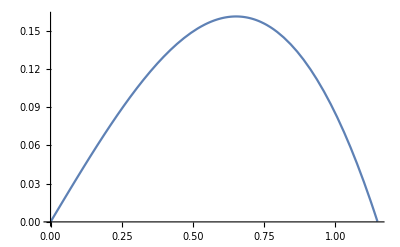

```mathematica
Plot[Evaluate[g[θ0,{g[0],g[1]}][θ]/.data2],{θ,0,1.148}]
```

```mathematica
s
```

s

```mathematica
(DufDuh[θ0,θYL,B,C0,CYL,{},{g[0]}])[2][R,θ]
```

(R^2 (-1+θ^2)^2 Log[R^2 (-1+θ^2)^2])/(8 π)+1/(RealAbs[R (-1+θ^2)]^(7/4))(1/((-(15 θ^2 (-1+θ^2) (1-θ^2/θ0^2) g[0])/(4 RealAbs[-1+θ^2]^(31/8))+((1-θ^2/θ0^2) g[0])/(RealAbs[-1+θ^2]^(15/8))-(2 θ^2 g[0])/(θ0^2 RealAbs[-1+θ^2]^(15/8)))^3)(-θ/(2 π (-1+θ^2))+(CYL (-(5 ⅈ)/(6 (-ⅈ θ+θYL)^(1/6))+(5 ⅈ)/(6 (ⅈ θ+θYL)^(1/6)))+(C0 (1-ⅇ^(-1/(B (-θ-θ0))) ExpIntegralEi[1/(B (-θ-θ0))]-(ⅇ^(-1/(B (-θ-θ0))) ExpIntegralEi[1/(B (-θ-θ0))])/(B (-θ-θ0))))/π+(C0 (-1+ⅇ^(-1/(B (θ-θ0))) ExpIntegralEi[1/(B (θ-θ0))]+(ⅇ^(-1/(B (θ-θ0))) ExpIntegralEi[1/(B (θ-θ0))])/(B (θ-θ0))))/π)/((-1+θ^2)^2)-(4 θ (CYL (-2 θYL^(5/6)+(-ⅈ θ+θYL)^(5/6)+(ⅈ θ+θYL)^(5/6))+(C0 (ⅇ^(-1/(B (-θ-θ0))) (-θ-θ0) ExpIntegralEi[1/(B (-θ-θ0))]+ⅇ^(1/(B θ0)) θ0 ExpIntegralEi[-1/(B θ0)]))/π+(C0 (ⅇ^(-1/(B (θ-θ0))) (θ-θ0) ExpIntegralEi[1/(B (θ-θ0))]+ⅇ^(1/(B θ0)) θ0 ExpIntegralEi[-1/(B θ0)]))/π))/((-1+θ^2)^3)) (-(465 θ^3 (-1+θ^2)^2 (1-θ^2/θ0^2) g[0])/(16 RealAbs[-1+θ^2]^(47/8))+(15 θ^3 (1-θ^2/θ0^2) g[0])/(2 RealAbs[-1+θ^2]^(31/8))+(45 θ (-1+θ^2) (1-θ^2/θ0^2) g[0])/(4 RealAbs[-1+θ^2]^(31/8))-(15 θ^3 (-1+θ^2) g[0])/(θ0^2 RealAbs[-1+θ^2]^(31/8))+(6 θ g[0])/(θ0^2 RealAbs[-1+θ^2]^(15/8)))+1/((-(15 θ^2 (-1+θ^2) (1-θ^2/θ0^2) g[0])/(4 RealAbs[-1+θ^2]^(31/8))+((1-θ^2/θ0^2) g[0])/(RealAbs[-1+θ^2]^(15/8))-(2 θ^2 g[0])/(θ0^2 RealAbs[-1+θ^2]^(15/8)))^2)(θ^2/(π (-1+θ^2)^2)-1/(2 π (-1+θ^2))+(CYL (5/(36 (-ⅈ θ+θYL)^(7/6))+5/(36 (ⅈ θ+θYL)^(7/6)))+(C0 (-1/(B (-θ-θ0)^2)-1/(-θ-θ0)+(ⅇ^(-1/(B (-θ-θ0))) ExpIntegralEi[1/(B (-θ-θ0))])/(B^2 (-θ-θ0)^3)))/π+(C0 (-1/(B (θ-θ0)^2)-1/(θ-θ0)+(ⅇ^(-1/(B (θ-θ0))) ExpIntegralEi[1/(B (θ-θ0))])/(B^2 (θ-θ0)^3)))/π)/((-1+θ^2)^2)-(8 θ (CYL (-(5 ⅈ)/(6 (-ⅈ θ+θYL)^(1/6))+(5 ⅈ)/(6 (ⅈ θ+θYL)^(1/6)))+(C0 (1-ⅇ^(-1/(B (-θ-θ0))) ExpIntegralEi[1/(B (-θ-θ0))]-(ⅇ^(-1/(B (-θ-θ0))) ExpIntegralEi[1/(B (-θ-θ0))])/(B (-θ-θ0))))/π+(C0 (-1+ⅇ^(-1/(B (θ-θ0))) ExpIntegralEi[1/(B (θ-θ0))]+(ⅇ^(-1/(B (θ-θ0))) ExpIntegralEi[1/(B (θ-θ0))])/(B (θ-θ0))))/π))/((-1+θ^2)^3)+(24 θ^2 (CYL (-2 θYL^(5/6)+(-ⅈ θ+θYL)^(5/6)+(ⅈ θ+θYL)^(5/6))+(C0 (ⅇ^(-1/(B (-θ-θ0))) (-θ-θ0) ExpIntegralEi[1/(B (-θ-θ0))]+ⅇ^(1/(B θ0)) θ0 ExpIntegralEi[-1/(B θ0)]))/π+(C0 (ⅇ^(-1/(B (θ-θ0))) (θ-θ0) ExpIntegralEi[1/(B (θ-θ0))]+ⅇ^(1/(B θ0)) θ0 ExpIntegralEi[-1/(B θ0)]))/π))/((-1+θ^2)^4)-(4 (CYL (-2 θYL^(5/6)+(-ⅈ θ+θYL)^(5/6)+(ⅈ θ+θYL)^(5/6))+(C0 (ⅇ^(-1/(B (-θ-θ0))) (-θ-θ0) ExpIntegralEi[1/(B (-θ-θ0))]+ⅇ^(1/(B θ0)) θ0 ExpIntegralEi[-1/(B θ0)]))/π+(C0 (ⅇ^(-1/(B (θ-θ0))) (θ-θ0) ExpIntegralEi[1/(B (θ-θ0))]+ⅇ^(1/(B θ0)) θ0 ExpIntegralEi[-1/(B θ0)]))/π))/((-1+θ^2)^3)))

```mathematica
χ0=Limit[(DufDuh[θ0,θYL,B,C0,CYL,{},{g[0],g[1]}])[2][R,θ],θ->θ0,Direction->"FromBelow",Assumptions->{θ0>1,R>0,B>0,θ0>0,θYL>0,g[0]>0,g[1]>0}]
```

1/(8 R^(7/4) g[0]^2)(-1+θ0^2) (-1/π+(2 θ0^2)/(π (-1+θ0^2))+(48 θ0^2 (CYL π (-2 θYL^(5/6)+(-ⅈ θ0+θYL)^(5/6)+(ⅈ θ0+θYL)^(5/6))+2 C0 ⅇ^(1/(B θ0)) θ0 ExpIntegralEi[-1/(B θ0)]-2 C0 ⅇ^(1/(2 B θ0)) θ0 ExpIntegralEi[-1/(2 B θ0)]))/(π (-1+θ0^2)^3)-(8 (CYL π (-2 θYL^(5/6)+(-ⅈ θ0+θYL)^(5/6)+(ⅈ θ0+θYL)^(5/6))+2 C0 ⅇ^(1/(B θ0)) θ0 ExpIntegralEi[-1/(B θ0)]-2 C0 ⅇ^(1/(2 B θ0)) θ0 ExpIntegralEi[-1/(2 B θ0)]))/(π (-1+θ0^2)^2)-(16 θ0 (C0/π-5/6 ⅈ CYL (1/(-ⅈ θ0+θYL)^(1/6)-1/(ⅈ θ0+θYL)^(1/6))-(C0 ⅇ^(1/(2 B θ0)) (-1+2 B θ0) ExpIntegralEi[-1/(2 B θ0)])/(2 B π θ0)))/((-1+θ0^2)^2)+(2 ((2 B C0)/π+5/36 CYL (1/(-ⅈ θ0+θYL)^(7/6)+1/(ⅈ θ0+θYL)^(7/6))+(C0 (2 B θ0 (-1+2 B θ0)-ⅇ^(1/(2 B θ0)) ExpIntegralEi[-1/(2 B θ0)]))/(8 B^2 π θ0^3)))/(-1+θ0^2)-(3 (2+3 θ0^2) ((θ0 (-1+θ0^2)^2)/π+(8 θ0 (CYL π (-2 θYL^(5/6)+(-ⅈ θ0+θYL)^(5/6)+(ⅈ θ0+θYL)^(5/6))+2 C0 ⅇ^(1/(B θ0)) θ0 ExpIntegralEi[-1/(B θ0)]-2 C0 ⅇ^(1/(2 B θ0)) θ0 ExpIntegralEi[-1/(2 B θ0)]))/π-2 (-1+θ0^2) (C0/π-5/6 ⅈ CYL (1/(-ⅈ θ0+θYL)^(1/6)-1/(ⅈ θ0+θYL)^(1/6))-(C0 ⅇ^(1/(2 B θ0)) (-1+2 B θ0) ExpIntegralEi[-1/(2 B θ0)])/(2 B π θ0))))/(2 θ0 (-1+θ0^2)^3))+(R^2 (-1+θ0^2)^2 Log[R (-1+θ0^2)])/(4 π)

```mathematica
1/(8 R^(7/4) g[0]^2)(-1+θ0^2) (-1/π+(2 θ0^2)/(π (-1+θ0^2))+(48 θ0^2 (CYL π (-2 θYL^(5/6)+(-ⅈ θ0+θYL)^(5/6)+(ⅈ θ0+θYL)^(5/6))+2 C0 ⅇ^(1/(B θ0)) θ0 ExpIntegralEi[-1/(B θ0)]-2 C0 ⅇ^(1/(2 B θ0)) θ0 ExpIntegralEi[-1/(2 B θ0)]))/(π (-1+θ0^2)^3)-(8 (CYL π (-2 θYL^(5/6)+(-ⅈ θ0+θYL)^(5/6)+(ⅈ θ0+θYL)^(5/6))+2 C0 ⅇ^(1/(B θ0)) θ0 ExpIntegralEi[-1/(B θ0)]-2 C0 ⅇ^(1/(2 B θ0)) θ0 ExpIntegralEi[-1/(2 B θ0)]))/(π (-1+θ0^2)^2)-(16 θ0 (C0/π-5/6 ⅈ CYL (1/(-ⅈ θ0+θYL)^(1/6)-1/(ⅈ θ0+θYL)^(1/6))-(C0 ⅇ^(1/(2 B θ0)) (-1+2 B θ0) ExpIntegralEi[-1/(2 B θ0)])/(2 B π θ0)))/((-1+θ0^2)^2)+(2 ((2 B C0)/π+5/36 CYL (1/(-ⅈ θ0+θYL)^(7/6)+1/(ⅈ θ0+θYL)^(7/6))+(C0 (2 B θ0 (-1+2 B θ0)-ⅇ^(1/(2 B θ0)) ExpIntegralEi[-1/(2 B θ0)]))/(8 B^2 π θ0^3)))/(-1+θ0^2)-(3 (2+3 θ0^2) ((θ0 (-1+θ0^2)^2)/π+(8 θ0 (CYL π (-2 θYL^(5/6)+(-ⅈ θ0+θYL)^(5/6)+(ⅈ θ0+θYL)^(5/6))+2 C0 ⅇ^(1/(B θ0)) θ0 ExpIntegralEi[-1/(B θ0)]-2 C0 ⅇ^(1/(2 B θ0)) θ0 ExpIntegralEi[-1/(2 B θ0)]))/π-2 (-1+θ0^2) (C0/π-5/6 ⅈ CYL (1/(-ⅈ θ0+θYL)^(1/6)-1/(ⅈ θ0+θYL)^(1/6))-(C0 ⅇ^(1/(2 B θ0)) (-1+2 B θ0) ExpIntegralEi[-1/(2 B θ0)])/(2 B π θ0))))/(2 θ0 (-1+θ0^2)^3))+(R^2 (-1+θ0^2)^2 Log[R (-1+θ0^2)])/(4 π)/.B->ruleB[θ0,{g[0]}]/.C0->ruleAL[θ0,{g[0]}]/.data2
```

(1.44368+0. ⅈ)/R^(7/4)+0.00809004 R^2 Log[0.318846 R]

```mathematica
Limit[(DufDut@@prep2)[2][R,θ],θ->θ]
```

```mathematica
ComplexPlot[(DufDut@@prep2)[θ],{θ,3}]
```

-Graphics-

```mathematica
(uf@@Most[prep2])[1,θ]
```

-0.172824 (-1.98276+(0.989667-ⅈ θ)^(5/6)+(0.989667+ⅈ θ)^(5/6))-0.310183 θ^2+0.247454 θ^4-0.00363798 (-1.84268+ⅇ^(-0.196535/(-1.14841-θ)) (-1.14841-θ) ExpIntegralEi[0.196535/(-1.14841-θ)])-0.00363798 (-1.84268+ⅇ^(-0.196535/(-1.14841+θ)) (-1.14841+θ) ExpIntegralEi[0.196535/(-1.14841+θ)])

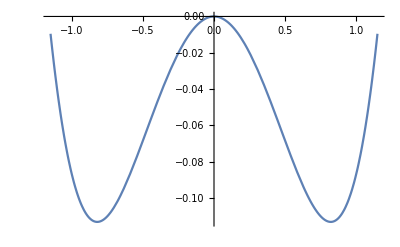

```mathematica
Plot[(uf@@Most[prep2])[1,θ],{θ,-1.148,1.148}]
```

```mathematica
test=DufDut[θ0,θYL,B,C0,CYL,{},{g[0]}][2][R,θ];
```

```mathematica
Series[test,{θ,0,0},Assumptions->{R>0,θ0>0,g[0]>1}]
```

(45-8 Log[θ^2 g[0]^2]+16 Log[R^(15/4) θ^2 g[0]^2])/(120 π)+O[θ]^1

```mathematica
Series[DScriptF0DηList[θ0,θYL,B,C0,CYL,{},{g[0]}][2,θ][[-1]],{θ,0,0},Assumptions->{R>0,θ0>0,g[0]>1}]
```

(45-8 Log[θ^2 g[0]^2])/(120 π)+O[θ]^1

```mathematica
8/60
```

2/15

```mathematica
16/120
```

2/15

```mathematica
D[96 B^2 θ0^3 θYL^(7/6) Log[θ^2 g[0]^2] θ^2,{θ,2}]
```

576 B^2 θ0^3 θYL^(7/6)+192 B^2 θ0^3 θYL^(7/6) Log[θ^2 g[0]^2]

```mathematica
Series[test,{θ,θ0,0},Assumptions->{R>0,θ0>0,g[0]>1}]
```

$Aborted

```mathematica
uf[θ0,θYL,B,C0,CYL,{}][R,θ]
```

R^2 (CYL (-2 θYL^(5/6)+(-ⅈ θ+θYL)^(5/6)+(ⅈ θ+θYL)^(5/6))+(C0 (ⅇ^(-1/(B (-θ-θ0))) (-θ-θ0) ExpIntegralEi[1/(B (-θ-θ0))]+ⅇ^(1/(B θ0)) θ0 ExpIntegralEi[-1/(B θ0)]))/π+(C0 (ⅇ^(-1/(B (θ-θ0))) (θ-θ0) ExpIntegralEi[1/(B (θ-θ0))]+ⅇ^(1/(B θ0)) θ0 ExpIntegralEi[-1/(B θ0)]))/π)+(R^2 (-1+θ^2)^2 Log[R^2])/(8 π)

```mathematica
Series[(1-1/(g[θ0,{g[0]}][θ])^(2/Δ)),{θ,0,1},Assumptions->{θ>0}]
```

1+θ^(-2/Δ) (-g[0]^(-2/Δ)+O[θ]^2)

```mathematica
dat=Flatten[Table[{ut[R,θ],uh[θ0,{g[0],g[1]}][R,θ],-(DufDuh@@prep2)[1][R,θ]}/.data2,{R,0.05,2,0.05},{θ,-1.14841,1.14841,0.05}],1];
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

```mathematica
ListPlot3D[dat]
```

-Graphics3D-

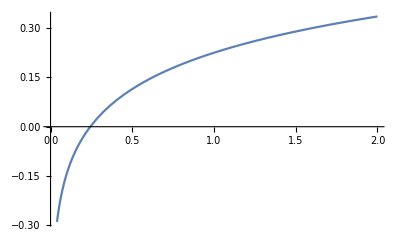

```mathematica
Plot[Evaluate[(DufDut@@prep2)[2][R,0.1]],{R,0,2}]
```

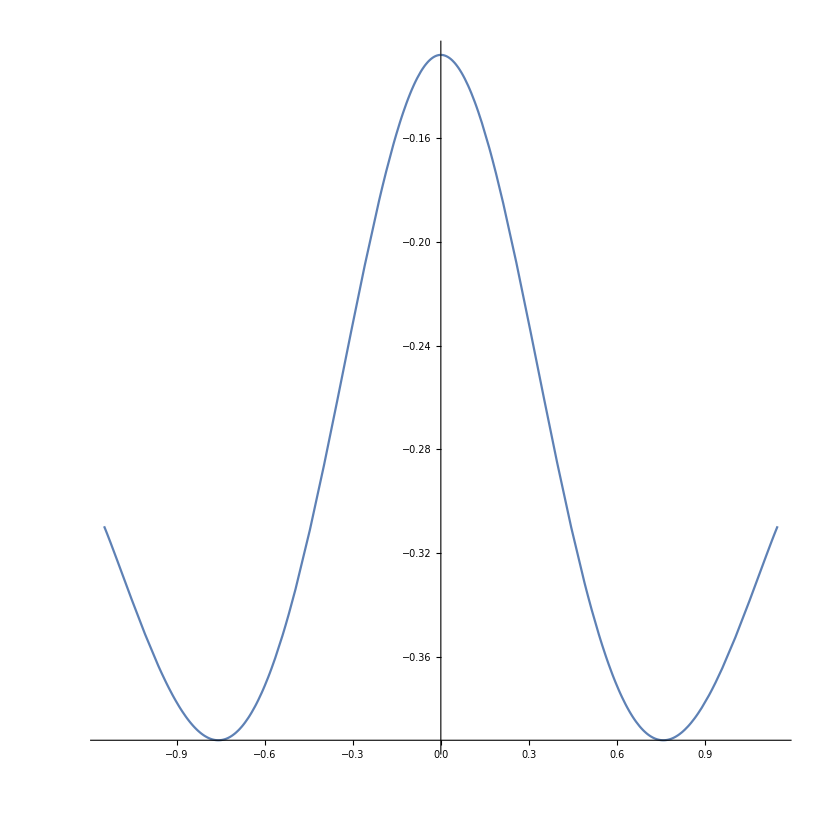

```mathematica
ParametricPlot[{θ,Evaluate[(DufDut@@prep2)[2][.1,θ]]},{θ,-1.148,1.148},AspectRatio->1]
```

```mathematica
dGdξ
```

```mathematica
(dΦdηList@@prep2)[0,1]
```

{-1.19741+0. ⅈ}

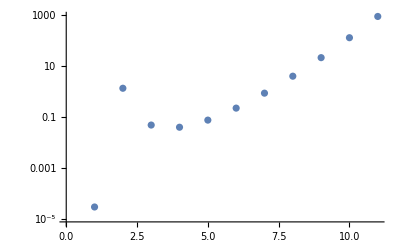

```mathematica
ListLogPlot[Abs[(DScriptFPlusMinusDξθ0List@@prep2)[10]]]
```

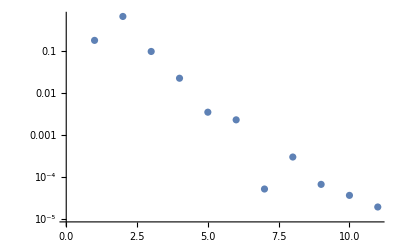

```mathematica
ListLogPlot[Abs[(DScriptF0DηList@@prep2)[10,0.5]]]
```